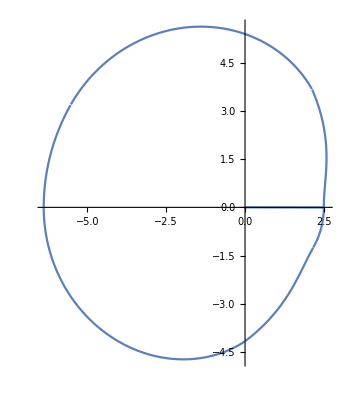

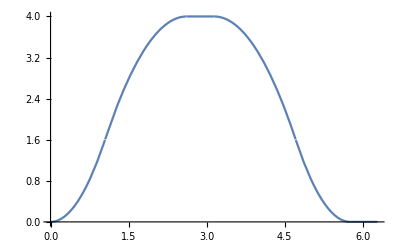

Power::infy: Infinite expression 1/0. encountered.

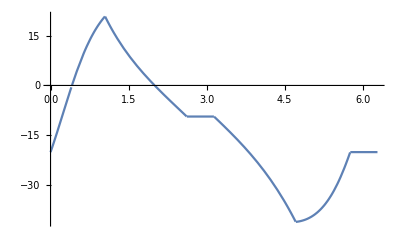

```mathematica
rp=3.5;
e=1.2;
rr=1;
θ=(θr*180)/π;
y1=(1.6/3600)*(θ^2);
y2=(((-1)/3375)*(θ^2))+((4/45)*θ)-(8/3);
y3=4;
y4=(((-1)/3375)*((330-θ)^2))+((4/45)*(330-θ))-(8/3);
y5=(1.6/3600)*((330-θ)^2);
y6=0;
y11=D[y1,θr];
y21=D[y2,θr];
y31=D[y3,θr];
y41=D[y4,θr];
y51=D[y5,θr];
y61=D[y6,θr];
ϕ1=ArcTan[(y11-e)/(y1+(((rp^2)-(e^2))^0.5))];
ϕ2=ArcTan[(y21-e)/(y2+(((rp^2)-(e^2))^0.5))];
ϕ3=ArcTan[(y31-e)/(y3+(((rp^2)-(e^2))^0.5))];
ϕ4=ArcTan[(y41-e)/(y4+(((rp^2)-(e^2))^0.5))];
ϕ5=ArcTan[(y51-e)/(y5+(((rp^2)-(e^2))^0.5))];
ϕ6=ArcTan[(y61-e)/(y6+(((rp^2)-(e^2))^0.5))];
rc1=((((((rp^2)-(e^2))^0.5)+y1-(rr*Cos[ϕ1]))^2)+((e+(rr*Sin[ϕ1]))^2))^0.5;
rc2=((((((rp^2)-(e^2))^0.5)+y2-(rr*Cos[ϕ2]))^2)+((e+(rr*Sin[ϕ2]))^2))^0.5;
rc3=((((((rp^2)-(e^2))^0.5)+y3-(rr*Cos[ϕ3]))^2)+((e+(rr*Sin[ϕ3]))^2))^0.5;
rc4=((((((rp^2)-(e^2))^0.5)+y4-(rr*Cos[ϕ4]))^2)+((e+(rr*Sin[ϕ4]))^2))^0.5;
rc5=((((((rp^2)-(e^2))^0.5)+y5-(rr*Cos[ϕ5]))^2)+((e+(rr*Sin[ϕ5]))^2))^0.5;
rc6=((((((rp^2)-(e^2))^0.5)+y6-(rr*Cos[ϕ6]))^2)+((e+(rr*Sin[ϕ6]))^2))^0.5;
rc=Piecewise[{{rc1,0≤θr≤(π/3)},{rc2,(π/3)<θr≤((5*π)/6)},{rc3,((5*π)/6)<θr≤π},{rc4,π<θr≤((3*π)/2)},{rc5,((3*π)/2)<θr≤((2*π)-(π/6))},{rc6,((2*π)-(π/6))<θr<(2*π)}}];
y=Piecewise[{{y1,0≤θr≤(π/3)},{y2,(π/3)<θr≤((5*π)/6)},{y3,((5*π)/6)<θr≤π},{y4,π<θr≤((3*π)/2)},{y5,((3*π)/2)<θr≤((2*π)-(π/6))},{y6,((2*π)-(π/6))<θr<(2*π)}}];
ϕ=Piecewise[{{ϕ1,0≤θr≤(π/3)},{ϕ2,(π/3)<θr≤((5*π)/6)},{ϕ3,((5*π)/6)<θr≤π},{ϕ4,π<θr≤((3*π)/2)},{ϕ5,((3*π)/2)<θr≤((2*π)-(π/6))},{ϕ6,((2*π)-(π/6))<θr<(2*π)}}];
PolarPlot[rc,{θr,0,(2*π)}]
Plot[y,{θr,0,(2*π)}]
Plot[((ϕ*180)/π),{θr,0,(2*π)}]
```